```mathematica
With[{folder="theory_dnn"},data=With[{fnames=FileNames["DOS_*.dat",folder]},PrintTemporary@Dynamic@{i,Length@fnames};With[{params=(#[[-2;;]]&)@*StringCases[RegularExpression["\\d+"]]/@fnames//ToExpression},Table[params[[i]]//Append[BinaryDeserialize@Get@fnames[[i]]],{i,Length@params}]]];dataTransition=With[{fnames=FileNames["transition_*.dat",folder]},PrintTemporary@Dynamic@{i,Length@fnames};With[{params=(#[[-1;;]]&)@*StringCases[RegularExpression["\\d+"]]/@fnames//ToExpression},Table[params[[i]]~Join~BinaryDeserialize@Get@fnames[[i]],{i,Length@params}]]];]
```

Randomly sample Jacobian matrices:

```mathematica
ClearAll[JacobianMatrix];JacobianMatrix[α_?NumericQ,g_?NumericQ,ϕ_,n_]:=With[{χFn=g ϕ'[#]&,χDist=StableDistribution[α,0,0,g(Abs[s]/2)^(1/α)/.FindRoot[Abs[s]-NExpectation[Abs[ϕ[h]]^α,h\[Distributed]StableDistribution[α,0,0,g(Abs[s]/2)^(1/α)]],{s,1,.5}]]},RandomVariate[StableDistribution[α,0,0,(2n)^(-1/α)],{n,n}].DiagonalMatrix[χFn@RandomVariate[χDist,n]]];
```

```mathematica
eigs120=With[{α=1.2,g=1.5},Quiet@Eigenvalues@JacobianMatrix[α,g,Tanh,2000]];
```

DOS_alpha_120_inset.pdf

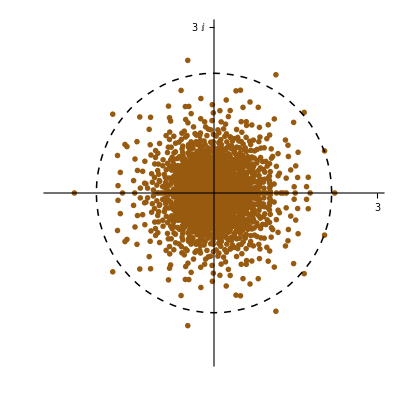

```mathematica
With[{radius=First@Cases[Sort@data,{120,150,DOS_}:>DOS[[-1,1]]],xLim=3},Show[ListPlot[ReIm@eigs120,PlotRange->{{-xLim,xLim},{-xLim,xLim}},PlotMarkers->{"OpenMarkers",Tiny},AspectRatio->1,PlotStyle->Darker@ColorData[98,"ColorList"][[2]],TicksStyle->Black,ImageSize->Tiny,PlotRangeClipping->False,Ticks->{{3},{{3,3ⅈ}}}]/.{p:_Disk|_Polygon:>{FaceForm[],p}},Graphics@{Black,AbsoluteThickness[1.1],Dashed,Circle[{0,0},radius]}]//EchoFunction[Export["DOS_alpha_120_inset.pdf",#]&]]
```

```mathematica
eigs200=With[{α=2,g=1.5},Quiet@Eigenvalues@JacobianMatrix[α,g,Tanh,2000]];
```

DOS_alpha_200_inset.pdf

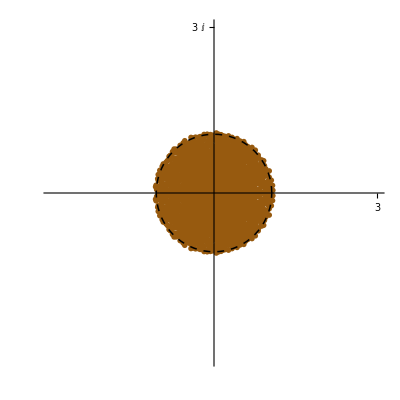

```mathematica
With[{radius=First@Cases[Sort@data,{200,150,DOS_}:>DOS[[-1,1]]],xLim=3},Show[ListPlot[ReIm@eigs200,PlotRange->{{-xLim,xLim},{-xLim,xLim}},PlotMarkers->{"OpenMarkers",Tiny},AspectRatio->1,PlotStyle->Darker@ColorData[98,"ColorList"][[2]],TicksStyle->Black,ImageSize->Tiny,PlotRangeClipping->False,Ticks->{{3},{{3,3ⅈ}}}]/.{p:_Disk|_Polygon:>{FaceForm[],p}},Graphics@{Black,AbsoluteThickness[1.1],Dashed,Circle[{0,0},radius]}]//EchoFunction[Export["DOS_alpha_200_inset.pdf",#]&]]
```

DOS_alpha_120.pdf

DOS_alpha_200.pdf

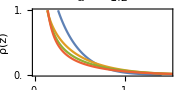
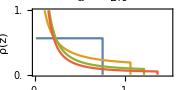

```mathematica
Table[ListLinePlot[Cases[Sort@data,{alpha100,g_,DOS_}:>Append[DOS,{DOS[[-1,1]],0}]][[15;;;;15]],ImageSize->Small,FrameStyle->Black,Frame->{True,True,False,False},FrameLabel->{"|z|","ρ(z)"},PlotLabel->Style[StringTemplate["α == ``"][alpha100/100.],Black],PlotRange->{{0,1.5},{0,1}},AspectRatio->.5,FrameTicks->{Range[0,1.5,.5],Range[0,1,.5]}]//EchoFunction[Export[StringTemplate["DOS_alpha_``.pdf"]@alpha100,#]&],{alpha100,{120,200}}]
```

Comparing Jacobian averages in an absolute sense (thus effectively ignoring eigenvector correlations)

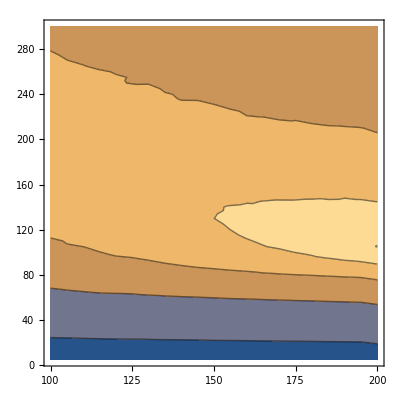
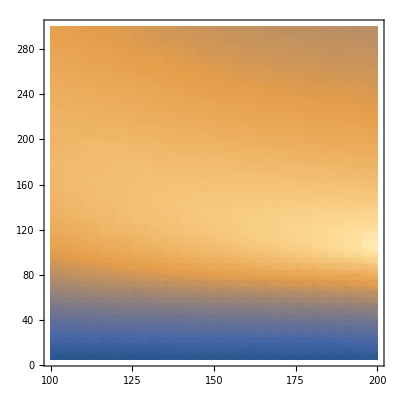
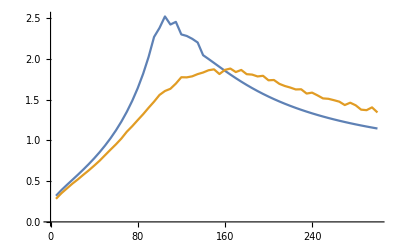
{-Graphics-,-Graphics-,-Graphics3D-,-Graphics3D-,-Graphics-}

```mathematica
#@With[{f=2π 0.01With[{λ=(#)+0Log[#]},Sign[λ]Abs[λ]^1]&,f2=0#^1+1(-1/Log@#)&},MapAt[f2@Total[#1f[#1]#2&@@@#]&,3]/@Cases[data,{_?(GreaterEqualThan[0]),_?(GreaterEqualThan[0]),_}]]&/@{ListContourPlot,ListDensityPlot,ListPointPlot3D,ListPlot3D,ListLinePlot@{Sort@Cases[#,{200,g_,jacAvg_}->{g,jacAvg}],Sort@Cases[#,{120,g_,jacAvg_}->{g,jacAvg}]}&}
```

Comparing Jacobian averages in a sense relative to its value at the edge of the ordered phase (to show the degree to which the critical regime performs better than the ordered edge)

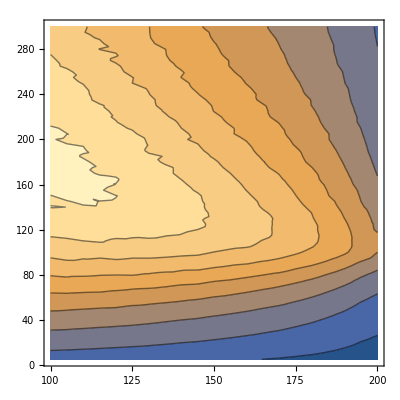
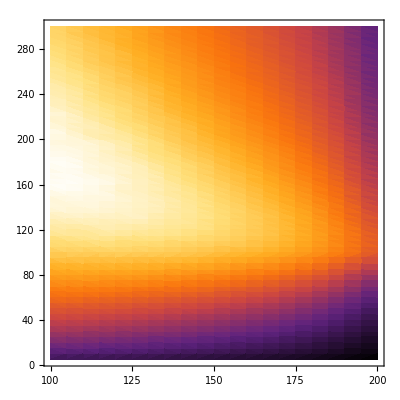
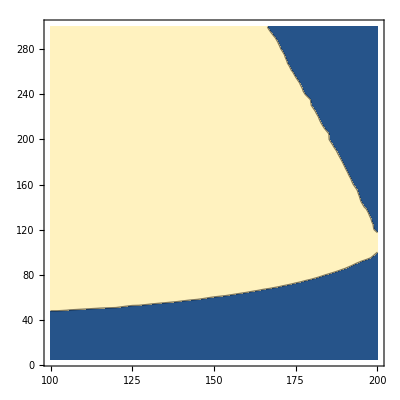
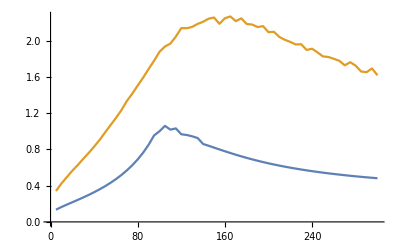
{-Graphics-,-Graphics-,-Graphics3D-,-Graphics3D-,-Graphics-,-Graphics-}

```mathematica
#@With[{f=2π 0.01With[{λ=1(#)+0Log[#]},Sign[λ]Abs[λ]^1]&,f2=0#^1+1(-1/Log@#)&},With[{jacTransition=MapAt[f2@Total[#1f[#1]#2&@@@#]&,3]/@dataTransition,jac=MapAt[f2@Total[#1f[#1]#2&@@@#]&,3]/@Cases[data,{_?(GreaterEqualThan[100]),_?(GreaterEqualThan[0]),_}]},{#1,#2,With[{transitionJacAvg=Cases[jacTransition,{#1,_,_}][[1,3]]},#3/transitionJacAvg]}&@@@jac]]&/@{ListContourPlot,ListDensityPlot[#,ColorFunction->"SunsetColors",ColorFunctionScaling->True]&,ListPointPlot3D,ListPlot3D,ListContourPlot[#,Contours->{1}]&,ListLinePlot@{Sort@Cases[#,{200,g_,jacAvg_}->{g,jacAvg}],Sort@Cases[#,{120,g_,jacAvg_}->{g,jacAvg}]}&}
```

```mathematica
LaunchKernels[7]//Length
```

7

```mathematica
DistributeDefinitions[data,dataTransition]
```

{data,dataTransition}

```mathematica
counter=0;SetSharedVariable[counter];PrintTemporary@Dynamic@{counter};(jacAverages=ParallelTable[counter++;Quiet@With[{f=With[{λ=1Log[#]+0(#-2)},Sign[λ]Abs[λ]^n]&},With[{jacTransition=MapAt[Total[#1f[#1]#2&@@@#]&,3]/@dataTransition,jac=MapAt[Total[#1f[#1]#2&@@@#]&,3]/@Cases[data,{_?(GreaterEqualThan[100]),_?(GreaterEqualThan[0]),_}]},{#1,#2,#3-Cases[jacTransition,{#1,_,_}][[1,3]]}&@@@jac]],{n,6Rest@Range[0,1,.01]}])//ByteCount
```

15137696

Use the logarithmic jacobian average to construct the colour gradient of the phase diagram schematic.

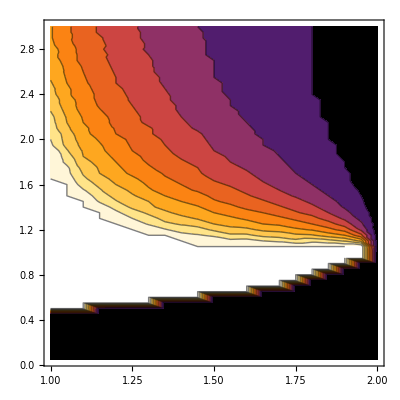
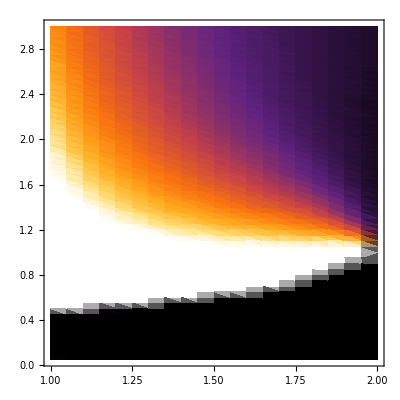
{-Graphics-,-Graphics-,-Graphics3D-,-Graphics3D-}

```mathematica
jacAverages//Transpose[#,{3,1,2}]&//Map[MapAt[First[#]/100&,{{1},{2}}]@*MapAt[First@FirstPosition[#,_?(LessThan[0]),{Length@#}]&,3]]//{ListContourPlot[#,ColorFunction->"SunsetColors"]&,ListDensityPlot[#,ColorFunction->"SunsetColors"]&,ListPointPlot3D,ListPlot3D[#,PlotRange->All]&}//Through
```

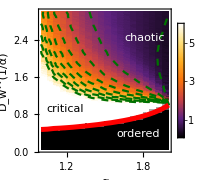

```mathematica
jacAverages//Transpose[#,{3,1,2}]&//Map[MapAt[First[#]/100&,{{1},{2}}]@*MapAt[First@FirstPosition[#,_?(LessThan[0]),{Length@#}]*(6*0.01)&,3]]//Show[ListDensityPlot[#,ColorFunction->"SunsetColors",ImageSize->Small,FrameLabel->{"α","D_w^(1/α)"},PlotLegends->BarLegend[Automatic,FrameStyle->Black,TicksStyle->Black],FrameStyle->Black],Table[Import[StringTemplate["phasediagram/pow_``.csv"]@n]//ListLinePlot[#,PlotStyle->{Darker@Darker@Green,Dashed}]&,{n,Range[1,100,10]}]//Append@ListLinePlot[Import["phasediagram/ordered.csv"],PlotStyle->{Red,Thickness[.02]}],Graphics@{Text[Style["ordered",White],Scaled@{.75,.125}],Text[Style["critical",Black],Scaled@{.2,.3}],Text[Style["chaotic",White],Scaled@{.8,.8}]}]&
```

```mathematica
Export["phasetransition_schematic.pdf",ResourceFunction["EvaluatePreviousCell"][],"AllowRasterization"->False]
```

phasetransition_schematic.pdf

Now overlay the above phase diagram schematic with lines based on the polynomial jacobian average. Save the lines for use in the other figures

```mathematica
ResourceFunction["EvaluatePreviousCell"][]//Export["transition.gif",#,"AnimationRepetitions"->∞]&
```

transition.gif

```mathematica
counter=0;SetSharedVariable[counter];PrintTemporary@Dynamic@{counter};ParallelTable[counter++;Quiet@With[{f=With[{λ=0Log[#]+1(#-2)},Sign[λ]Abs[λ]^n]&},With[{jacTransition=MapAt[Total[#1f[#1]#2&@@@#]&,3]/@dataTransition,jac=MapAt[Total[#1f[#1]#2&@@@#]&,3]/@Cases[data,{_?(GreaterEqualThan[100]),_?(GreaterEqualThan[100]),_}]},{#1,#2,#3-Cases[jacTransition,{#1,_,_}][[1,3]]}&@@@jac]]//ListContourPlot[#,PlotLabel->n,Contours->{0}]&//Cases[Normal@#,Line[pts__]->pts,Infinity]&//First//Export[StringTemplate["phasediagram/pow_``.csv"]@n,#/100.]&,{n,Rest@Range[0,101,1]}]
```

{phasediagram/pow_1.csv,phasediagram/pow_2.csv,phasediagram/pow_3.csv,phasediagram/pow_4.csv,phasediagram/pow_5.csv,phasediagram/pow_6.csv,phasediagram/pow_7.csv,phasediagram/pow_8.csv,phasediagram/pow_9.csv,phasediagram/pow_10.csv,phasediagram/pow_11.csv,phasediagram/pow_12.csv,phasediagram/pow_13.csv,phasediagram/pow_14.csv,phasediagram/pow_15.csv,phasediagram/pow_16.csv,phasediagram/pow_17.csv,phasediagram/pow_18.csv,phasediagram/pow_19.csv,phasediagram/pow_20.csv,phasediagram/pow_21.csv,phasediagram/pow_22.csv,phasediagram/pow_23.csv,phasediagram/pow_24.csv,phasediagram/pow_25.csv,phasediagram/pow_26.csv,phasediagram/pow_27.csv,phasediagram/pow_28.csv,phasediagram/pow_29.csv,phasediagram/pow_30.csv,phasediagram/pow_31.csv,phasediagram/pow_32.csv,phasediagram/pow_33.csv,phasediagram/pow_34.csv,phasediagram/pow_35.csv,phasediagram/pow_36.csv,phasediagram/pow_37.csv,phasediagram/pow_38.csv,phasediagram/pow_39.csv,phasediagram/pow_40.csv,phasediagram/pow_41.csv,phasediagram/pow_42.csv,phasediagram/pow_43.csv,phasediagram/pow_44.csv,phasediagram/pow_45.csv,phasediagram/pow_46.csv,phasediagram/pow_47.csv,phasediagram/pow_48.csv,phasediagram/pow_49.csv,phasediagram/pow_50.csv,phasediagram/pow_51.csv,phasediagram/pow_52.csv,phasediagram/pow_53.csv,phasediagram/pow_54.csv,phasediagram/pow_55.csv,phasediagram/pow_56.csv,phasediagram/pow_57.csv,phasediagram/pow_58.csv,phasediagram/pow_59.csv,phasediagram/pow_60.csv,phasediagram/pow_61.csv,phasediagram/pow_62.csv,phasediagram/pow_63.csv,phasediagram/pow_64.csv,phasediagram/pow_65.csv,phasediagram/pow_66.csv,phasediagram/pow_67.csv,phasediagram/pow_68.csv,phasediagram/pow_69.csv,phasediagram/pow_70.csv,phasediagram/pow_71.csv,phasediagram/pow_72.csv,phasediagram/pow_73.csv,phasediagram/pow_74.csv,phasediagram/pow_75.csv,phasediagram/pow_76.csv,phasediagram/pow_77.csv,phasediagram/pow_78.csv,phasediagram/pow_79.csv,phasediagram/pow_80.csv,phasediagram/pow_81.csv,phasediagram/pow_82.csv,phasediagram/pow_83.csv,phasediagram/pow_84.csv,phasediagram/pow_85.csv,phasediagram/pow_86.csv,phasediagram/pow_87.csv,phasediagram/pow_88.csv,phasediagram/pow_89.csv,phasediagram/pow_90.csv,phasediagram/pow_91.csv,phasediagram/pow_92.csv,phasediagram/pow_93.csv,phasediagram/pow_94.csv,phasediagram/pow_95.csv,phasediagram/pow_96.csv,phasediagram/pow_97.csv,phasediagram/pow_98.csv,phasediagram/pow_99.csv,phasediagram/pow_100.csv,phasediagram/pow_101.csv}

```mathematica
Cases[Most/@dataTransition,{alpha100_?(GreaterEqualThan[100]),g_}->{alpha100/100.,g}]//Sort//Export["phasediagram/ordered.csv",#]&
```

phasediagram/ordered.csv

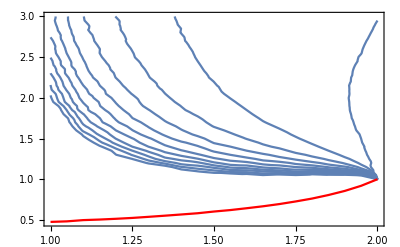

```mathematica
Show[Table[Import[StringTemplate["phasediagram/pow_``.csv"]@n]//ListLinePlot,{n,Range[1,101,10]}]//Append@ListLinePlot[Import["phasediagram/ordered.csv"],PlotStyle->Red],PlotRange->All,Frame->True]
```

```mathematica
counter=0;SetSharedVariable[counter];PrintTemporary@Dynamic@{counter};ParallelTable[counter++;Quiet@With[{f=With[{λ=0Log[#]+1(#-2)},Sign[λ]Abs[λ]^n]&},With[{jacTransition=MapAt[Total[#1f[#1]#2&@@@#]&,3]/@dataTransition,jac=MapAt[Total[#1f[#1]#2&@@@#]&,3]/@Cases[data,{_?(GreaterEqualThan[100]),_?(GreaterEqualThan[0]),_}]},{#1,#2,#3-Cases[jacTransition,{#1,_,_}][[1,3]]}&@@@jac]]//ListContourPlot[#,PlotLabel->n,Contours->{0}]&//Rasterize,{n,1Rest@Range[0,500,1]}]//ListAnimate[#,AnimationRunning->False]&
```

## Functions in the batch script

```mathematica
JacobianDOSVectorSave[alpha100_,g100_]:=With[{fname=StringTemplate["theory_dnn/DOS_alpha_``_g_``.dat"][alpha100,g100]},If[Not@MemberQ[FileNames["*.dat","theory_dnn"],fname],Put[BinarySerialize@If[alpha100==200,JacobianDOSGaussianVector[g100/100.],JacobianDOSVector[alpha100/100.,g100/100.,0.01]],fname]]]
```

```mathematica
JacobianDOSVector[α_?NumericQ,g_?NumericQ,yFrac_?NumericQ,ϕ_:Tanh,nSamples_:100000,δr_:0.01]:=With[{χFn=g ϕ'[#]&,χDist=StableDistribution[α,0,0,g(Abs[s]/2)^(1/α)/.FindRoot[Abs[s]-NExpectation[Abs[ϕ[h]]^α,h\[Distributed]StableDistribution[α,0,0,g(Abs[s]/2)^(1/α)]],{s,1,.5}]]},DOSVector[α,yFrac,χDist,χFn,nSamples,δr]];
```

```mathematica
DOSVector[α_?NumericQ,yFrac_?NumericQ,χDist_,χFn_,nSamples_:100000,δr_:.01]:=With[{SDistSamples=RandomVariate[SDist[α],nSamples],y0=((4 Cos[(π α)/4] Csc[(π α)/2] Sin[(π α)/4])/Gamma[1+α])^(1/α)},With[{samples={SDistSamples,RandomSample@SDistSamples,χFn@RandomVariate[χDist,nSamples]}},Table[r~List~With[{y=Abs[y]/.FindRoot[1-Mean[((#3^2#1)/(r^2+#3^2y^2#1 #2))^(α/2)&~MapThread~samples],{y,1,0.5}]},With[{δy=-Mean[((#3^2#1)^(α/2))/((r^2+#3^2y^2#1 #2)^(α/2+1))&~MapThread~samples]/Mean[((#3^2#1)/(r^2+#3^2y^2#1 #2))^(α/2+1)2y#2&~MapThread~samples]},(y^2-2 r^2 y δy)/π Mean[(#3^2#1#2)/((r^2+#3^2y^2#1 #2)^2)&~MapThread~samples]]],{r,δr,Abs@z/.Quiet@FindRoot[1-Mean[((#3^2#1)/(z^2+#3^2(yFrac y0)^2#1 #2))^(α/2)&~MapThread~samples],{z,1,2}],δr}]]]
```

```mathematica
JacobianOrderedTransitionSave[alpha100_,nReps_:1]:=With[{fname=StringTemplate["theory_dnn/transition_alpha_``.dat"][alpha100]},If[Not@MemberQ[FileNames["transition_*.dat","theory_dnn"],fname],Put[BinarySerialize@If[alpha100==200,{1,Table[{r,N[1/π]},{r,.01,.99,.01}]},With[{g=JacobianOrderedTransition[alpha100/100.,0.01,Tanh,nReps]},{g,JacobianDOSVector[alpha100/100.,g,0.01,Tanh]}]],fname]]]
```

```mathematica
JacobianOrderedTransitionEqnRHS[α_?NumericQ,yFrac_?NumericQ,ϕ_,g_?NumericQ,nReps_:1]:=With[{y0=((4 Cos[(π α)/4] Csc[(π α)/2] Sin[(π α)/4])/Gamma[1+α])^(1/α),χFn=g ϕ'[#]&,χDist=StableDistribution[α,0,0,g(Abs[s]/2)^(1/α)/.(*FindRoot[Abs[s]-NExpectation[Abs[ϕ[h]]^α,h\[Distributed]StableDistribution[α,0,0,g(Abs[s]/2)^(1/α)]],{s,1,.5}]*)With[{samples=RandomVariate[StableDistribution[α,0,0,(1/2)^(1/α)],10000]},FindRoot[Abs[s]-Mean[Abs[ϕ[g Abs[s]^(1/α)#]]^α&~Map~samples],{s,1,.5}]]]},Mean@Table[NExpectation[((χFn[χ]^2 S)/(1+(yFrac y0)^2 χFn[χ]^2 S Sp))^(α/2),{S\[Distributed]SDist[α],Sp\[Distributed]SDist[α],χ\[Distributed]χDist},Method->"MonteCarlo"],nReps](*This has poor accuracy: With[{nSamples=100000},With[{samples={RandomVariate[SDist[α],nSamples],RandomVariate[SDist[α],nSamples],χFn@RandomVariate[χDist,nSamples]}},Mean[((#3^2#1)/(1+#3^2(yFrac y0)^2#1 #2))^(α/2)&~MapThread~samples]]]*)];JacobianOrderedTransition[α_?NumericQ,yFrac_?NumericQ,ϕ_:Tanh,nReps_:1]:=Abs@g/.FindRoot[1-JacobianOrderedTransitionEqnRHS[α,yFrac,ϕ,Abs@g,nReps],{g,1,.5}]
```

```mathematica
SDist[α_]:=With[{C=Function[α1,Gamma[1+α1]Sin[π α1/2]/π]},StableDistribution[α/2,1,0,(C[α]/(4C[α/2]))^(2/α)]]
```

```mathematica
ClearAll[yStarGaussian];yStarGaussian[z_?NumericQ,χDist_,χFn_]:=With[{α=2,S=1,Sp=1},Abs@yStar/.FindRoot[1-NExpectation[((χFn[χ]^2 S)/(z^2+yStar^2 χFn[χ]^2 S Sp))^(α/2),χ\[Distributed]χDist],{yStar,1,.5}]]
```

```mathematica
ClearAll[DOSGaussian];DOSGaussian[z_?NumericQ,χDist_,χFn_]:=With[{yStar=yStarGaussian[z,χDist,χFn],α=2,S=1,Sp=1},With[{δyStar=-(NExpectation[((χFn[χ]^2 S)^(α/2))/((z^2+yStar^2 χFn[χ]^2 S Sp)^(α/2+1)),χ\[Distributed]χDist]/NExpectation[((χFn[χ]^2 S)^(α/2+1)2yStar Sp)/((z^2+yStar^2 χFn[χ]^2 S Sp)^(α/2+1)),χ\[Distributed]χDist])},(yStar^2-2 z^2 yStar δyStar)/π NExpectation[(χFn[χ]^2 S Sp)/((z^2+yStar^2 χFn[χ]^2 S Sp)^2),χ\[Distributed]χDist]]]
```

```mathematica
ClearAll[JacobianDOSGaussianVector];JacobianDOSGaussianVector[g_?NumericQ,ϕ_:Tanh,δr_:0.01]:=With[{α=2},With[{χFn=g ϕ'[#]&,χDist=StableDistribution[α,0,0,g(Abs[s]/2)^(1/α)/.FindRoot[Abs[s]-NExpectation[Abs[ϕ[h]]^α,h\[Distributed]StableDistribution[α,0,0,g(Abs[s]/2)^(1/α)]],{s,1,.5}]]},Table[{z,DOSGaussian[z,χDist,χFn]},{z,δr,NExpectation[χFn[χ]^2,χ\[Distributed]χDist]^(1/2),δr}]]];
```